```mathematica
(*The goal of this is to simulate the Sun and the eight planets, in three dimensions, as accurately as possible.*)
```

```mathematica
(*First Cell: Equations of Motion*)
Remove["Global`*"]

SetAttributes[{M,G,m1,m2,m3,m4,m5,m6,m7,m8,m9},Constant]; 
$Assumptions = {Element[{G,m1,m2,m3,m4,m5,m6,m7,m8,m9},Reals] && G>0 };

(*Nine Bodies including the Sun, six degrees of freedom*)
NumOfBodies =9;
m ={m1,m2,m3,m4,m5,m6,m7,m8,m9};
x={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t]};
y={y1[t],y2[t],y3[t],y4[t],y5[t],y6[t],y7[t],y8[t],y9[t]};
z={z1[t],z2[t],z3[t],z4[t],z5[t],z6[t],z7[t],z8[t],z9[t]};
dxdt={x1'[t],x2'[t],x3'[t],x4'[t],x5'[t],x6'[t],x7'[t],x8'[t],x9'[t]};
dydt={y1'[t],y2'[t],y3'[t],y4'[t],y5'[t],y6'[t],y7'[t],y8'[t],y9'[t]};
dzdt={z1'[t],z2'[t],z3'[t],z4'[t],z5'[t],z6'[t],z7'[t],z8'[t],z9'[t]};

(*Lagrangian*)
T[i_] := 1/2*m[[i]]*(dxdt[[i]]^2+dydt[[i]]^2+dzdt[[i]]^2);
TSum :=Sum[T[i],{i,1,NumOfBodies}];

U[i_,j_]:=-G*m[[i]]*m[[j]]/(Sqrt[(x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2+(z[[i]]-z[[j]])^2]);
USum := Sum[ Sum[U[i,j],{j,i+1,NumOfBodies}], {i,1,NumOfBodies}];

lag=TSum-USum;

(*Euler-Lagrange to find the Equations of Motion*)
EL[q_] :=  D[lag,q] - Dt[   D[lag,  D[q,t]], t ] == 0;

ELX[i_]:=EL[x[[i]]]
EqnsOfMotionX=Array[ELX,NumOfBodies];
ELY[i_]:=EL[y[[i]]];
EqnsOfMotionY=Array[ELY,NumOfBodies];
ELZ[i_]:=EL[z[[i]]];
EqnsOfMotionZ=Array[ELZ,NumOfBodies];
```

```mathematica
(*Second Cell: Orbital Parameters*)
(*J2000 Epoch, but disregarding anomaly*)

G=6.6743*10^-20;(*km^2 kg^-1 s^-1*)

(*Data from https://nssdc.gsfc.nasa.gov/planetary/factsheet/*)
(*All in kilograms*)
m1=0.330*10^24;(*Mercury*)
m2=4.870*10^24;(*Venus*)
m3=5.970*10^24;(*Earth*)
m4=0.642*10^24;(*Mars*)
m5=1898.*10^24;(*Jupiter*)
m6=568.0*10^24;(*Saturn*)
m7=86.80*10^24;(*Uranus*)
m8=102.0*10^24;(*Neptune*)
m9=1.990*10^30;(*Sun*)

Perihelion = {
46.002*10^6,
107.476*10^6,
147.092*10^6,
206.617*10^6,
740.522*10^6,
1352.555*10^6,
2741.302*10^6,
4444.449*10^6,
0.0001
};

MaxVelocity={
58.98,
35.26,
30.29,
26.50,
13.72,
10.18,
7.11,
5.50,
0.0001
};

Inclination={
7.00487,
3.39471,
0.00005,
1.85061,
1.30530,
2.48446,
0.76986,
1.76917,
0.0001
};
Inclination = Inclination *2*Pi/360;

LongAscNode={   
48.33167,
76.68069,
348.73936,
49.57854,
100.55615,
113.71504,
74.22988,
131.72169,
0
};
LongAscNode=LongAscNode*2*Pi/360;

LongPeri={
77.45645,
131.53298,
102.94719,
336.04084,
14.75385,
92.43194,
170.96424,
44.97135,
1.23456
};
LongPeri=LongPeri*2*Pi/360;
```

```mathematica
(*Parameter Conversions*)
ArgOfPeri=LongPeri-LongAscNode;

(*Planet Orbital Parameters, All in km and km/s*)
x0=Perihelion*(Cos[ArgOfPeri]*Cos[LongAscNode]-Sin[ArgOfPeri]*Cos[Inclination]*Sin[LongAscNode]);
y0=Perihelion*(Cos[ArgOfPeri]*Sin[LongAscNode]+Sin[ArgOfPeri]*Cos[Inclination]*Cos[LongAscNode]);
z0=Perihelion*Sin[ArgOfPeri]*Sin[Inclination];


vx0=-y0^2-z0^2;
vy0=x0*y0;
vz0=x0*z0;
mag=Sqrt[vx0^2+vy0^2+vz0^2];
vx0=vx0*MaxVelocity/mag;
vy0=vy0*MaxVelocity/mag;
vz0=vz0*MaxVelocity/mag;

(*If planet is in lower quadrants, velocity vector must flip*)
For[i=1,i<=NumOfBodies,i++,
If[y0[[i]]<0,{vx0[[i]]*=-1,vy0[[i]]*=-1,vz0[[i]]*=-1}];
];

InitialConditions={};

For[i=1,i<=NumOfBodies,i++,
AppendTo[InitialConditions,{x[[i]]/.t->0}==x0[[i]]];
AppendTo[InitialConditions,{y[[i]]/.t->0}==y0[[i]]];
AppendTo[InitialConditions,{z[[i]]/.t->0}==z0[[i]]];
AppendTo[InitialConditions,{dxdt[[i]]/.t->0}==vx0[[i]]];
AppendTo[InitialConditions,{dydt[[i]]/.t->0}==vy0[[i]]];
AppendTo[InitialConditions,{dzdt[[i]]/.t->0}==vz0[[i]]];
];
```

```mathematica
(*Solving the Equations of Motion*)
EndTime=100*31557600;(*Years*)
TimeStep=10;(*Seconds*)
numeric=NDSolve[{EqnsOfMotionX,EqnsOfMotionY,EqnsOfMotionZ,InitialConditions},{x,y,z},{t,0,EndTime,TimeStep}][[1]];

xSoln[t_]=x/.numeric;//Simplify 
ySoln[t_]=y/.numeric;//Simplify  
zSoln[t_]=z/.numeric;//Simplify
```

```mathematica
(*Animating the Solar System*)
Mercury[t_]:=Graphics3D[{PointSize[0.01],Brown,Point[{xSoln[t][[1]],ySoln[t][[1]],zSoln[t][[1]]}]}];
Venus[t_]:=     Graphics3D[{PointSize[0.01],Orange,Point[{xSoln[t][[2]],ySoln[t][[2]],zSoln[t][[2]]}]}];
Earth[t_]:=     Graphics3D[{PointSize[0.01],Cyan,Point[{xSoln[t][[3]],ySoln[t][[3]],zSoln[t][[3]]}]}];
Mars[t_]:=       Graphics3D[{PointSize[0.01],Red,Point[{xSoln[t][[4]],ySoln[t][[4]],zSoln[t][[4]]}]}];
Jupiter[t_]:=Graphics3D[{PointSize[0.01],Orange,Point[{xSoln[t][[5]],ySoln[t][[5]],zSoln[t][[5]]}]}];
Saturn[t_]:=  Graphics3D[{PointSize[0.01],Brown,Point[{xSoln[t][[6]],ySoln[t][[6]],zSoln[t][[6]]}]}];
Uranus[t_]:=  Graphics3D[{PointSize[0.01],Cyan,Point[{xSoln[t][[7]],ySoln[t][[7]],zSoln[t][[7]]}]}];
Neptune[t_]:=Graphics3D[{PointSize[0.01],Blue,Point[{xSoln[t][[8]],ySoln[t][[8]],zSoln[t][[8]]}]}];
Sun[t_]:=         Graphics3D[{PointSize[0.02],Yellow,Point[{xSoln[t][[9]],ySoln[t][[9]],zSoln[t][[9]]}]}];

SolarSystem[t_]={Sun[t],Mercury[t],Venus[t],Earth[t],Mars[t],Jupiter[t],Saturn[t],Uranus[t],Neptune[t]};
WideView[t_]:=Show[SolarSystem[t],Axes->False,PlotRange->{{-5*10^9,5*10^9},{-5*10^9,5*10^9},{-5*10^9,5*10^9}},Background->Black,ImageSize->Medium,AxesOrigin->{0,0}];
InnerPlanets[t_]:=Show[SolarSystem[t],Axes->False,PlotRange->{{-3*10^8,3*10^8},{-3*10^8,3*10^8},{-3*10^8,3*10^8}},Background->Black,ImageSize->Medium,AxesOrigin->{0,0}];

Year =31557600;
t1=100*Year;
Animate[WideView[t],{t,0,t1,TimeStep},AnimationRunning->False,AnimationRate->365*86400]
t2=10*Year;
Animate[InnerPlanets[t],{t,0,t2,TimeStep},AnimationRunning->False,AnimationRate->30*86400]
```

The above two animations show the Solar System, the first one with the Sun and all eight planets and the second one with the Sun and just the four inner planets. All planet sizes are clearly not to scale, but distances are indeed to scale.

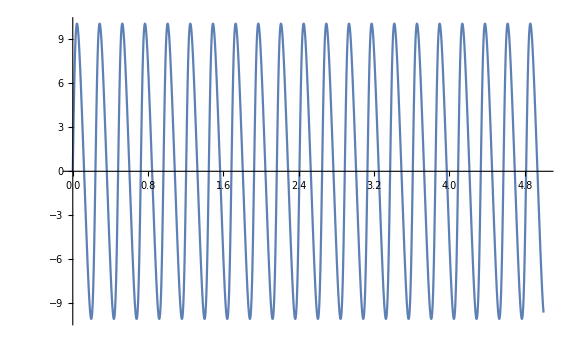

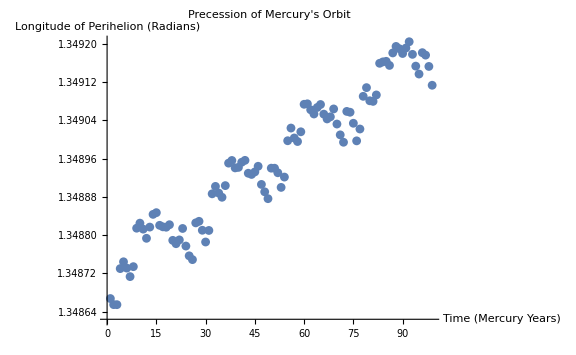

```mathematica
(*This is for Mercury and the Sun, but can easily be modified for other planet by changing the numbers in only the line below*)
RadialDistance[t_]=Sqrt[(xSoln[t][[1]]-xSoln[t][[9]])^2+(ySoln[t][[1]]-ySoln[t][[9]])^2+(zSoln[t][[1]]-zSoln[t][[9]])^2] ;
RadialVelocity[t_] = D[RadialDistance[t],t];
Plot[RadialVelocity[t*Year],{t,0,5}]

(*Apsides occur when velocity is zero. Every other apside is a perihelion.*)
PeriTimes={};
Period= 87.969*86400; (*Mercury Year*)
For[i=1,i<100,i++,
AppendTo[PeriTimes,t/.FindRoot[RadialVelocity[t],{t,Period*(i-0.2),Period*(i+0.2)}]]
]

(*Plotting the longitude of perihelion over time*)
PeriLongitude[t_]=ArcTan[xSoln[t][[1]]-xSoln[t][[9]],ySoln[t][[1]]-ySoln[t][[9]]];
PeriTable = Table[PeriLongitude[t],{t,PeriTimes}];
ListPlot[PeriTable,AxesLabel->{"Time (Mercury Years)","Longitude of Perihelion (Radians)"},PlotLabel->"Precession of Mercury's Orbit",ImageSize->Large]
```

```mathematica
(*Running a Fit to find the rate of Mercury's precession*)

TruePeriod= {};
For[i=1,i<49,i++,
AppendTo[TruePeriod,PeriTimes[[i+1]]-PeriTimes[[i]]]
];
MercuryYear=Mean[TruePeriod]

Precession = D[Fit[PeriTable, {1,t},t],t] (*Radians/Mercury Year*)
Precession = Precession * (360/(2*Pi)) * (1/MercuryYear)*(100*Year) *(3600); (*Converted to Arcseconds/Century*)

Print["Mercury's Precessional Rate: ", Precession," Arcseconds per Century"]
```

7.59759×10^6

4.92283×10^-6

Mercury's Precessional Rate: 421.763 Arcseconds per Century